```mathematica
(*Данные*)
f[x_]:=(x-0.5)^2; A=0; B=1; l1=B-A;
```

```mathematica
(*Метод дихотомии*)
ε=0.001; δ=0.01ε;    a=A;b=B; l=l1; k=1; L[k]=l;
While[l>ε,  x1=(a+b)/2-δ;   x2=(a+b)/2+δ;   If[f[x1]≥f[x2],a=x1,b=x2];  l=b-a; k++; L[k]=l; ];  x=(a+b)/2; K=k-1;
Print["Точка минимума:",x];    Print["Количество итераций:", K];     Print["Количество вычисленных значений функции:", 2K];
```

Точка минимума:0.500488

Количество итераций:10

Количество вычисленных значений функции:20

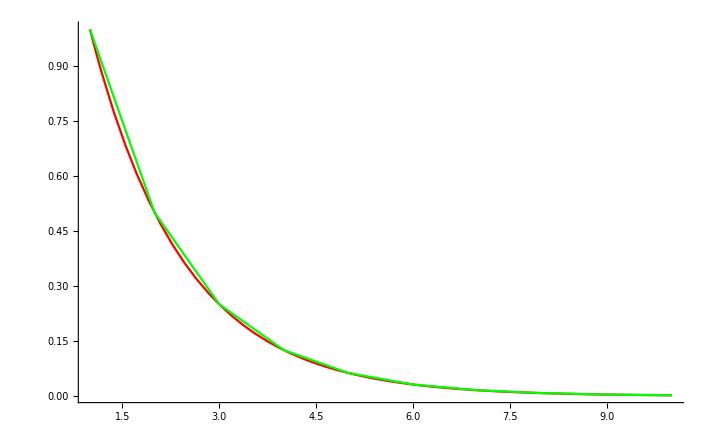

```mathematica
(*График убывания интервала неопределенности: аналитически и численно построенный*)
Anal=Plot[(l1-2δ)/2^(t-1)+2δ,{t,1,K},PlotStyle->Red,AxesOrigin->{0,0},PlotRange->All];
Num=ListLinePlot[Table[{i,L[i]},{i,1,K}],PlotStyle->Green,AxesOrigin->{0,0},PlotRange->All];
Show[Anal,Num]
```

```mathematica
(*Метод золотого сечения*)
ε=0.00001;   a=A;b=B; l1=B-A;  l=l1; k=1; L[k]=l;
κ=(√5-2)/2//N;δ=κ l;  x1=(a+b)/2-δ;   x2=(a+b)/2+δ; f1=f[x1]; f2=f[x2];
While[l>ε, 
If[f1≥f2,
a=x1;  x1=x2;   l=b-a;  δ=κ l;  x2=(a+b)/2+δ;  f1=f2; f2=f[x2],   
b=x2;  x2=x1;   l=b-a;  δ=κ l;  x1=(a+b)/2-δ;  f2=f1;  f1=f[x1]
]; 
k++; L[k]=l;
];
x=(a+b)/2; K=k-1;
Print["Точка минимума:",x];    Print["Количество итераций:", K];     Print["Количество вычисленных значений функции:", K+1];
```

Точка минимума:0.5

Количество итераций:24

Количество вычисленных значений функции:25

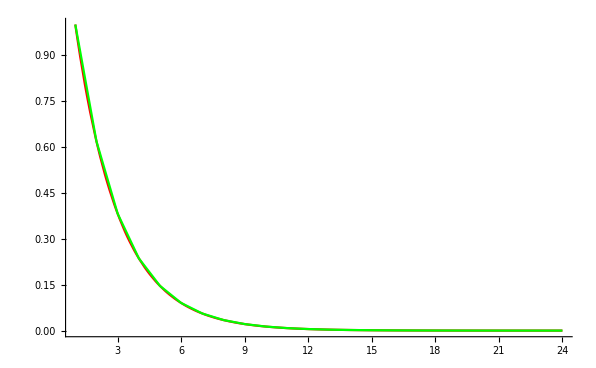

```mathematica
(*График убывания интервала неопределенности: аналитически и численно построенный*)
Anal=Plot[l1((√5-1)/2)^(t-1),{t,1,K},PlotStyle->Red,AxesOrigin->{0,0},PlotRange->All];
Num=ListLinePlot[Table[{i,L[i]},{i,1,K}],PlotStyle->Green,AxesOrigin->{0,0},PlotRange->All];
Show[Anal,Num]
```